# Runge Kutta 4th order method for ODE2

The main reason that Euler' s method (RK 1st) has such a large truncation error per step is that in evolving the solution from x_n to x_(n+1). 
The method only evaluates derivatives at the beginning of the interval : i.e., at x_n. Therefore, the method is very asymmetric with respect to the beginning and the end of the interval.We can construct a more symmetric integration method by making an Euler - like trial step to the midpoint of the interval, and then using the values of both x and y at the midpoint to make the real step across the interval.

## 1 st Order ODE

a dx/dt+b x = f[t],  x[t_0]=x_0
The time step is h
change the equation in to the form
dx/dt=F[t,x]
Runge Kutta 4th order method is
dx_1=h k_1=h F[t,x]
k_2=F[t+h/2,x+dx_1/2=x+k_1 h/2] a new estimation of the slop at position t+h/2
k_3=F[t+h/2, x+k_2 h/2] 2nd new estimation of the slop at t+h/2
k_4=F[t+h, x + k_3 h] final estimation of the slop at t+h
dx=h/6(k_1+2 k_2+2 k_3+k_4)  
x[t+h]=x[t] +dx

### Example

dx/dt+5x=Sin[t], x[0]=0
dx/dt=F[t,x]=Sin[t]-5x

{1/6,31}

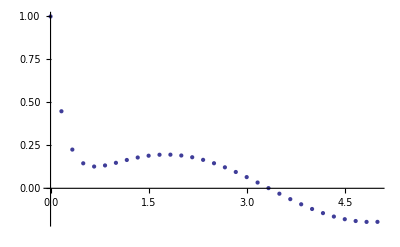

```mathematica
F[t_,x_]:=N[Sin[t]-5x]
k={0,0,0,0};
tRange={0,5};
nStep=30;
h=(tRange[[2]]-tRange[[1]])/nStep;
Sol=Table[{t,0},{t,tRange[[1]],tRange[[2]],h}];
Sol[[1,2]]=1;
Print[{h,Length[Sol]}];
Monitor[Table[
k[[1]]=F[Sol[[i,1]],Sol[[i,2]]];
k[[2]]=F[Sol[[i,1]]+h/2,Sol[[i,2]]+k[[1]] h/2];
k[[3]]=F[Sol[[i,1]]+h/2,Sol[[i,2]]+k[[2]] h/2];
k[[4]]=F[Sol[[i,1]]+h,Sol[[i,2]]+k[[3]] h];
dx=h/6(k[[1]]+2k[[2]]+2k[[3]]+k[[4]]);
Sol[[i+1,2]]=Sol[[i,2]]+dx;
(*Print[{k,dx,Sol[[i]]}];*)
,{i,1,nStep}],i];
g1=ListPlot[Sol]
```

{{X[t]→1. ⅇ^(-5. t)}}

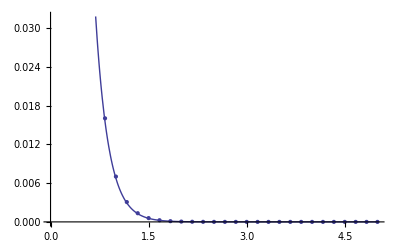

0. | 1. | 1 | 0.
0.166667 | 0.434598 | 0.437532 | -0.00293394
0.333333 | 0.188876 | 0.191434 | -0.00255878
0.5 | 0.082085 | 0.0837587 | -0.0016737
0.666667 | 0.035674 | 0.0366471 | -0.000973129
0.833333 | 0.0155039 | 0.0160343 | -0.000530441
1. | 0.00673795 | 0.00701552 | -0.000277572
1.16667 | 0.0029283 | 0.00306952 | -0.000141216
1.33333 | 0.00127263 | 0.00134301 | -0.0000703778
1.5 | 0.000553084 | 0.000587611 | -0.0000345264
1.66667 | 0.000240369 | 0.000257099 | -0.0000167291
1.83333 | 0.000104464 | 0.000112489 | -8.02476×10^-6
2. | 0.0000453999 | 0.0000492175 | -3.81758×10^-6
2.16667 | 0.0000197307 | 0.0000215342 | -1.80352×10^-6
2.33333 | 8.57494×10^-6 | 9.42192×10^-6 | -8.46985×10^-7
2.5 | 3.72665×10^-6 | 4.12239×10^-6 | -3.95741×10^-7
2.66667 | 1.6196×10^-6 | 1.80368×10^-6 | -1.84083×10^-7
2.83333 | 7.03874×10^-7 | 7.89168×10^-7 | -8.52942×10^-8
3. | 3.05902×10^-7 | 3.45286×10^-7 | -3.93841×10^-8
3.16667 | 1.32945×10^-7 | 1.51074×10^-7 | -1.81293×10^-8
3.33333 | 5.77775×10^-8 | 6.60997×10^-8 | -8.3222×10^-9
3.5 | 2.511×10^-8 | 2.89207×10^-8 | -3.81075×10^-9
3.66667 | 1.09128×10^-8 | 1.26538×10^-8 | -1.741×10^-9
3.83333 | 4.74266×10^-9 | 5.53642×10^-9 | -7.93759×10^-10
4. | 2.06115×10^-9 | 2.42236×10^-9 | -3.6121×10^-10
4.16667 | 8.95774×10^-10 | 1.05986×10^-9 | -1.64088×10^-10
4.33333 | 3.89302×10^-10 | 4.63724×10^-10 | -7.4422×10^-11
4.5 | 1.6919×10^-10 | 2.02894×10^-10 | -3.37042×10^-11
4.66667 | 7.35296×10^-11 | 8.87726×10^-11 | -1.52431×10^-11
4.83333 | 3.19558×10^-11 | 3.88409×10^-11 | -6.88506×10^-12
5. | 1.38879×10^-11 | 1.69941×10^-11 | -3.10619×10^-12

{0.0000192885}

```mathematica
s=DSolve[{X'[t]==F[t,X[t]],X[0]==Sol[[1,2]]},X[t],t]
ExSol[t_]:=Evaluate[X[t]/.s]
Show[
Plot[ExSol[t],{t,tRange[[1]],tRange[[2]]}],
g1
]
ListOfError=Table[{Sol[[i,1]]//N,ExSol[Sol[[i,1]]]//N,Sol[[i,2]],(ExSol[Sol[[i,1]]]//N)-Sol[[i,2]]},{i,1,Length[Sol]}];
ListOfError//TableForm
SSR=Sum[ListOfError[[i,4]]^2,{i,1,Length[Sol]}]
```

## 2nd Order ODE

(d^2 x)/dt^2+a dx/dt+ b x = f[t],  x[t_0]=x_0, dx[t_0]/dt=v[t_0]=v_0
The time step is h
change the equation in to the form
dv/dt=F[t,x,v]=f[t]-b x-a v
Runge Kutta 4th order method is
dx_1=h k_x1=h v,   dv_1=h k_v1=h F[t,x] 
dx_2=h k_x2=h (v+dv_1/2),  dv_2=h k_v2=h F[t+h/2,x+ dx_1/2, v+dv_1/2] 
dx_3=h k_x3=h (v+dv_2/2),  dv_3=h k_v3=h F[t+h/2,x+ dx_2/2, v+dv_2/2]
dx_4=h k_x4=h (v+dv_3),  dv_4=h k_v4=h F[t+h,x+ dx_3, v+dv_3]
dx=1/6(dx_1+2 dx_2+2 dx_3+dx_4),  dv=1/6(dv_1+2 dv_2+2 dv_3+dv_4)   
x[t+h]=x[t] +dx,  v[t+h]=v[t]+dv

### Example

(d^2 x)/dt^2+dx/dt+6x=Sin[t], x[0]=0, x'[0]=1
dx/dt=G[t,x]=6x - v

```mathematica
RK4ODE2[U_Symbol,T_,l_,u0_,v0_,ρRange_,nStep_]:=Module[
{G,kv,kx,h,Sol,dx,dv},
G[ρ_,u_,v_]:=U[ρ,u,v];
kv={0,0,0,0};
kx={0,0,0,0};
h=(ρRange[[2]]-ρRange[[1]])/nStep;
Sol=Table[{ρ,0,0},{ρ,ρRange[[1]],ρRange[[2]],h}];
Sol[[1,2]]=u0;
Sol[[1,3]]=v0;
Print[{h,Length[Sol]}];
Monitor[Table[
kv[[1]]=G[Sol[[i,1]],Sol[[i,2]],Sol[[i,3]]];
kx[[1]]=Sol[[i,3]];
kv[[2]]=G[Sol[[i,1]]+h/2,Sol[[i,2]]+kx[[1]] h/2, Sol[[i,3]]+kv[[1]] h/2];
kx[[2]]=Sol[[i,3]]+kv[[1]] h/2;
kv[[3]]=G[Sol[[i,1]]+h/2,Sol[[i,2]]+kx[[2]] h/2, Sol[[i,3]]+kv[[2]] h/2];
kx[[3]]=Sol[[i,3]]+kv[[2]] h/2;
kv[[4]]=G[Sol[[i,1]]+h,Sol[[i,2]]+kx[[3]] h, Sol[[i,3]]+kv[[3]] h];
kx[[4]]=Sol[[i,3]]+kv[[3]]h;
dx=h/6(kx[[1]]+2kx[[2]]+2kx[[3]]+kx[[4]]);
dv=h/6(kv[[1]]+2kv[[2]]+2kv[[3]]+kv[[4]]);
Sol[[i+1,3]]=Sol[[i,3]]+dv;
Sol[[i+1,2]]=Sol[[i,2]]+dx;
(*Print[{k,dx,Sol[[i]]}];*)
,{i,1,nStep}],i];
Print[
ListPlot[
Table[Sol[[i,1;;2]],{i,1,Length[Sol]}]
,Joined->True,PlotMarkers->Automatic]];
Sol
]
```

{1/8,41}

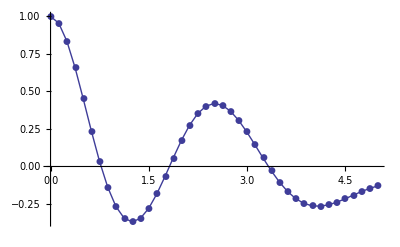

```mathematica
KK[ρ_,u_,v_]:=N[Sin[ρ]-6 u - v];
InitCon={1,0};
tRange={0,5};
PP=RK4ODE2[KK,1,1,InitCon[[1]],InitCon[[2]],tRange,40];
```

{{X[t]→ⅇ^(-0.5 t) ((1.03846+0. ⅈ) Cos[2.39792 t]-(0.0384615+0. ⅈ) ⅇ^(0.5 t) Cos[t] Cos[2.39792 t]^2+(0.192308+0. ⅈ) ⅇ^(0.5 t) Cos[2.39792 t]^2 Sin[t]+(0.136336+0. ⅈ) Sin[2.39792 t]-(0.0384615+0. ⅈ) ⅇ^(0.5 t) Cos[t] Sin[2.39792 t]^2+(0.192308+5.78744×10^-18 ⅈ) ⅇ^(0.5 t) Sin[t] Sin[2.39792 t]^2)}}

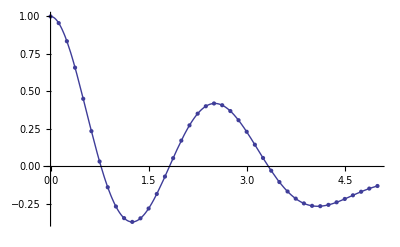

0. | 1.+0. ⅈ | 1 | 0.+0. ⅈ
0.125 | 0.95568+6.29082×10^-20 ⅈ | 0.955698 | -0.000018595+6.29082×10^-20 ⅈ
0.25 | 0.834835+4.55804×10^-19 ⅈ | 0.834876 | -0.0000409349+4.55804×10^-19 ⅈ
0.375 | 0.65881+1.29909×10^-18 ⅈ | 0.658871 | -0.0000609916+1.29909×10^-18 ⅈ
0.5 | 0.451211+2.40837×10^-18 ⅈ | 0.451284 | -0.0000737383+2.40837×10^-18 ⅈ
0.625 | 0.235545+3.36864×10^-18 ⅈ | 0.23562 | -0.0000757725+3.36864×10^-18 ⅈ
0.75 | 0.0331549+3.74402×10^-18 ⅈ | 0.0332205 | -0.0000656533+3.74402×10^-18 ⅈ
0.875 | -0.138418+3.317×10^-18 ⅈ | -0.138374 | -0.0000439465+3.317×10^-18 ⅈ
1. | -0.266543+2.23204×10^-18 ⅈ | -0.26653 | -0.0000130029+2.23204×10^-18 ⅈ
1.125 | -0.344049+9.63263×10^-19 ⅈ | -0.344073 | 0.000023475+9.63263×10^-19 ⅈ
1.25 | -0.369224+1.1341×10^-19 ⅈ | -0.369285 | 0.0000610021+1.1341×10^-19 ⅈ
1.375 | -0.345337+1.36237×10^-19 ⅈ | -0.345432 | 0.0000949373+1.36237×10^-19 ⅈ
1.5 | -0.27978+1.11619×10^-18 ⅈ | -0.279901 | 0.000121084+1.11619×10^-18 ⅈ
1.625 | -0.182943+2.71403×10^-18 ⅈ | -0.183079 | 0.000136199+2.71403×10^-18 ⅈ
1.75 | -0.0669553+4.3082×10^-18 ⅈ | -0.0670937 | 0.00013835+4.3082×10^-18 ⅈ
1.875 | 0.0555759+5.26739×10^-18 ⅈ | 0.0554488 | 0.000127109+5.26739×10^-18 ⅈ
2. | 0.17273+5.22595×10^-18 ⅈ | 0.172627 | 0.000103542+5.22595×10^-18 ⅈ
2.125 | 0.274241+4.23328×10^-18 ⅈ | 0.274171 | 0.0000700465+4.23328×10^-18 ⅈ
2.25 | 0.35221+2.70976×10^-18 ⅈ | 0.35218 | 0.0000300373+2.70976×10^-18 ⅈ
2.375 | 0.401533+1.23577×10^-18 ⅈ | 0.401545 | -0.0000124618+1.23577×10^-18 ⅈ
2.5 | 0.420031+2.80178×10^-19 ⅈ | 0.420085 | -0.0000532694+2.80178×10^-19 ⅈ
2.625 | 0.408324+3.6781×10^-22 ⅈ | 0.408412 | -0.0000884922+3.6781×10^-22 ⅈ
2.75 | 0.36946+2.06948×10^-19 ⅈ | 0.369574 | -0.000114916+2.06948×10^-19 ⅈ
2.875 | 0.308393+5.01542×10^-19 ⅈ | 0.308524 | -0.000130306+5.01542×10^-19 ⅈ
3. | 0.231352+5.09522×10^-19 ⅈ | 0.231486 | -0.000133585+5.09522×10^-19 ⅈ
3.125 | 0.145169+8.40768×10^-20 ⅈ | 0.145294 | -0.000124891+8.40768×10^-20 ⅈ
3.25 | 0.0566416-6.23864×10^-19 ⅈ | 0.0567471 | -0.000105501-6.23864×10^-19 ⅈ
3.375 | -0.0280302-1.26359×10^-18 ⅈ | -0.0279526 | -0.0000776466-1.26359×10^-18 ⅈ
3.5 | -0.103687-1.49578×10^-18 ⅈ | -0.103642 | -0.0000442499-1.49578×10^-18 ⅈ
3.625 | -0.16651-1.20252×10^-18 ⅈ | -0.166502 | -8.60212×10^-6-1.20252×10^-18 ⅈ
3.75 | -0.214174-5.81364×10^-19 ⅈ | -0.2142 | 0.0000259722-5.81364×10^-19 ⅈ
3.875 | -0.245843-6.79783×10^-20 ⅈ | -0.2459 | 0.0000564331-6.79783×10^-20 ⅈ
4. | -0.262052-1.20856×10^-19 ⅈ | -0.262132 | 0.000080296-1.20856×10^-19 ⅈ
4.125 | -0.264469-9.7498×10^-19 ⅈ | -0.264565 | 0.0000958306-9.7498×10^-19 ⅈ
4.25 | -0.255602-2.49128×10^-18 ⅈ | -0.255704 | 0.000102176-2.49128×10^-18 ⅈ
4.375 | -0.238462-4.18428×10^-18 ⅈ | -0.238561 | 0.0000993635-4.18428×10^-18 ⅈ
4.5 | -0.216224-5.42306×10^-18 ⅈ | -0.216312 | 0.0000882558-5.42306×10^-18 ⅈ
4.625 | -0.191924-5.71371×10^-18 ⅈ | -0.191994 | 0.0000704094-5.71371×10^-18 ⅈ
4.75 | -0.168198-4.92891×10^-18 ⅈ | -0.168246 | 0.0000478842-4.92891×10^-18 ⅈ
4.875 | -0.147096-3.37314×10^-18 ⅈ | -0.147119 | 0.0000230177-3.37314×10^-18 ⅈ
5. | -0.12997-1.65045×10^-18 ⅈ | -0.129968 | -1.80943×10^-6-1.65045×10^-18 ⅈ

{2.70674×10^-7-3.24422×10^-22 ⅈ}

```mathematica
s=DSolve[{X''[t]==KK[t,X[t],X'[t]],X[0]==InitCon[[1]],X'[0]==InitCon[[2]]},X[t],t]
ExSol[t_]:=Evaluate[X[t]/.s]
Show[
Plot[ExSol[t],{t,tRange[[1]],tRange[[2]]}],
ListPlot[
Table[PP[[i,{1,2}]],{i,1,Length[PP]}]
]
]
ListOfError=Table[{PP[[i,1]]//N,ExSol[PP[[i,1]]]//N,PP[[i,2]],(ExSol[PP[[i,1]]]//N)-PP[[i,2]]},{i,1,Length[PP]}];
ListOfError//TableForm
SSR=Sum[ListOfError[[i,4]]^2,{i,1,Length[PP]}]
```